# Generic Natario warp drive and deflector shield with no time dependence

## Geometric quantities

### Base quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

ClearAll[gLL];
gLL=FullSimplify[Inverse[gUU]];
```

### ADM quantities

```mathematica
ClearAll[scoordsU];
scoordsU=coordsU[[2;;4]];

ClearAll[γLL,γUU];
γLL=gLL[[2;;4,2;;4]];
γUU=FullSimplify[Inverse[γLL]];

ClearAll[lapse];
lapse=Simplify[Sqrt[-1/gUU[[1,1]]],α[t,x,y,z]>=0];

ClearAll[βU,βL];
βU=gUU[[1,2;;4]]α[t,x,y,z]^2;
βL=gLL[[1,2;;4]];

ClearAll[KLL];
KLL=Table[
1/(2lapse)(D[βL[[j]],scoordsU[[i]]]+D[βL[[i]],scoordsU[[j]]]),
{i,1,3},
{j,1,3}
]//FullSimplify;

ClearAll[nU,nL];
nU=Join[{1/lapse},-βU/lapse];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

### 4-Christoffel symbols

```mathematica
ClearAll[Γ];
Γ=Table[
FullSimplify[
(1/2)*Sum[
(gUU[[i,s]])*(D[gLL[[s,j]],coordsU[[k]] ]+D[gLL[[s,k]],coordsU[[j]] ]-D[gLL[[j,k]],coordsU[[s]] ]),
{s,1,4}
]
],
{i,1,4},
{j,1,4},
{k,1,4}
] ;
```

## Vincent Geodesic equations

```mathematica
ClearAll[VU];
VU={velx,vely,velz};

ClearAll[dXudt];
dXudt=FullSimplify[
Table[
lapse*VU[[i]]-βU[[i]],
{i,1,3}
]
];

ClearAll[dVUdt];
dVUdt=FullSimplify[
Table[
Sum[lapse*VU[[j]]VU[[i]]D[Log[lapse],scoordsU[[j]]],{j,1,3}]
-Sum[lapse*VU[[j]]VU[[i]]KLL[[j,k]]VU[[k]],{j,1,3},{k,1,3}]
+2Sum[lapse*VU[[j]]γUU[[i,k]]KLL[[k,j]],{k,1,3},{j,1,3}]
-Sum[γUU[[i,j]]D[lapse,scoordsU[[j]]],{j,1,3}]
-Sum[VU[[j]]D[βU[[i]],scoordsU[[j]]],{j,1,3}]
,
{i,1,3}
]
];

ClearAll[dEdt];
dEdt=FullSimplify[
energy(Sum[lapse*KLL[[j,k]]VU[[j]]VU[[k]],{j,1,3},{k,1,3}]-Sum[VU[[j]]D[lapse,scoordsU[[j]]],{j,1,3}])
];
```

```mathematica
ClearAll[vincentPU]
vincentPU=energy(nU+Join[{0},VU]);

ClearAll[vincentNorm]
vincentNorm=FullSimplify[Solve[Sum[gLL[[a,b]]vincentPU[[a]]vincentPU[[b]],{a,1,4},{b,1,4}]==(-δ),energy]]
```

{{energy→-(√δ)/(√(1-velx^2-vely^2-velz^2))},{energy→(√δ)/(√(1-velx^2-vely^2-velz^2))}}

## Transition function

```mathematica
ClearAll[deg,poly];
deg=7;
poly[x_]=Sum[c[i]x^i,{i,0,deg}];

ClearAll[polyCs];
polyCs=Solve[
{
poly[x0]==y0,
poly[x0+dx]==0,
Derivative[1][poly][x0]==0,
Derivative[1][poly][x0+dx]==0,
Derivative[2][poly][x0]==0,
Derivative[2][poly][x0+dx]==0,
Derivative[3][poly][x0]==0,
Derivative[3][poly][x0+dx]==0
},
Table[c[i],{i,0,deg}]
]//Flatten//FullSimplify;

ClearAll[polyWithCs];
polyWithCs=FullSimplify[poly[x]//.polyCs];

ClearAll[polyTrans];
polyTrans[x_,y0_,x0_,dx_]=Piecewise[
{
{y0,x<x0},
{0,x>(x0+dx)},
{polyWithCs,True}
}
]
```

Piecewise[{{y0, x<x0}, {0, x>dx+x0}, {((dx^3+4 dx^2 (x-x0)+10 dx (x-x0)^2+20 (x-x0)^3) (dx-x+x0)^4 y0)/dx^7, True}}]

```mathematica
D[polyTrans[x,y0,x0,dx],x]//FullSimplify
```

Piecewise[{{0, x<x0||dx+x0<x}, {-(140 (x-x0)^3 (dx-x+x0)^3 y0)/dx^7, True}}]

## Validation

```mathematica
ClearAll[α];
α[t_,x_,y_,z_]:=1

ClearAll[r,ρy,ρz];
r[t_,x_,y_,z_]:=Sqrt[((x-u*t)^2+y^2+z^2)]
ρy[y_,z_]:=y/Sqrt[y^2+z^2];
ρz[y_,z_]:=z/Sqrt[y^2+z^2];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]:=u0*f[r[t,x,y,z],1,radius,sigma];

vy[t_,x_,y_,z_]:=k0*ρy[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

vz[t_,x_,y_,z_]:=k0*ρz[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

ClearAll[f];
f[x_,y0_,x0_,dx_]=polyTrans[x,y0,x0,dx];

ClearAll[rule];
rule={
radius->4,
sigma->4,
DeflectorPushout->1,
DeflectorSigmaFactor->19/10,

u->88/100,
u0->0,
k0->0.719118,

t->0,
x->-9.7949469215078,
y->5.333823512281447,
z->0,
velx->u,
vely->-0.4749736834813107,
velz->0,
energy->2260313.7603819715
};

Print["dXdt = ",dXudt[[1]]//.rule//N]
Print["dYdt = ",dXudt[[2]]//.rule]
Print["dZdt = ",dXudt[[3]]//.rule]

Print["dVXdt = ",dVUdt[[1]]//.rule]
Print["dVYdt = ",dVUdt[[2]]//.rule]
Print["dVZdt = ",dVUdt[[3]]//.rule]

Print["E = ",dEdt//.rule]

Print["vx = ",vx[t,x,y,z]//.rule]
Print["d_vx_dx = ",D[vx[t,x,y,z],x]//.rule]
Print["d_vx_dy = ",D[vx[t,x,y,z],y]//.rule]
Print["d_vx_dz = ",D[vx[t,x,y,z],z]//.rule]

Print["vy = ",vy[t,x,y,z]//.rule]
Print["d_vy_dx = ",D[vy[t,x,y,z],x]//.rule]
Print["d_vy_dy = ",D[vy[t,x,y,z],y]//.rule]
Print["d_vy_dz = ",D[vy[t,x,y,z],z]//.rule]

Print["vz = ",vz[t,x,y,z]//.rule]
Print["d_vz_dx = ",D[vz[t,x,y,z],x]//.rule]
Print["d_vz_dy = ",D[vz[t,x,y,z],y]//.rule]
Print["d_vz_dz = ",D[vz[t,x,y,z],z]//.rule]

ClearAll[rule];
ClearAll[f];
ClearAll[vx,vy,vz];
ClearAll[r,ρy,ρz];
ClearAll[α];
```

dXdt = 0.88

dYdt = 0.0146775

dZdt = 0.

dVXdt = -0.00015878

dVYdt = -0.000294178

dVZdt = 0.

E = 203446.

vx = 0

d_vx_dx = 0

d_vx_dy = 0

d_vx_dz = 0

vy = 0.489651

d_vy_dx = 0.166426

d_vy_dy = -0.090627

d_vy_dz = 0.

vz = 0.

d_vz_dx = 0.

d_vz_dy = 0.

d_vz_dz = 0.0918012

## Fixed points

```mathematica
ClearAll[α];
α[t_,x_,y_,z_]:=1

ClearAll[r,ρy,ρz];
r[t_,x_,y_,z_]:=Sqrt[((x-u*t)^2+y^2+z^2)]
ρy[y_,z_]:=y/Sqrt[y^2+z^2];
ρz[y_,z_]:=z/Sqrt[y^2+z^2];

ClearAll[vx,vy,vz];
vx[t_,x_,y_,z_]:=u0*f[r[t,x,y,z],1,radius,sigma];

vy[t_,x_,y_,z_]:=k0*ρy[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

vz[t_,x_,y_,z_]:=k0*ρz[y,z]*(
f[r[t,x,y,z]-(radius+DeflectorPushout*sigma),1,0,DeflectorSigmaFactor*sigma]*f[(radius+DeflectorPushout*sigma)-r[t,x,y,z],1,0,DeflectorSigmaFactor*sigma]
);

ClearAll[rule];
rule={
u0->0,

t->0,
z->0,

velx->u,
velz->0
};

Print["dXdt = ",FullSimplify[dXudt[[1]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dYdt = ",FullSimplify[dXudt[[2]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dZdt = ",FullSimplify[dXudt[[3]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]

Print["dVXdt = ",FullSimplify[dVUdt[[1]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dVYdt = ",FullSimplify[dVUdt[[2]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]
Print["dVZdt = ",FullSimplify[dVUdt[[3]]//.rule,{x∈Reals,y∈Reals,z∈Reals}]]

Print["E = ",dEdt//.rule]

ClearAll[rule];
ClearAll[vx,vy,vz];
ClearAll[r,ρy,ρz];
ClearAll[α];
```

dXdt = u

dYdt = vely+k0 f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Sign[y]

dZdt = 0

dVXdt = -1/(√(x^2+y^2))k0 vely ((-1+u^2) x+u vely y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])

dVYdt = -1/(√(x^2+y^2))k0 vely (u vely x+(-1+vely^2) y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])

dVZdt = 0

E = -energy (u vely (-1/(√(y^2) √(x^2+y^2))k0 x y f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]+1/(√(y^2) √(x^2+y^2))k0 x y f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])+vely^2 (-1/(√(x^2+y^2))k0 √(y^2) f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]+1/(√(x^2+y^2))k0 √(y^2) f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] f^(1,0,0,0)[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]))

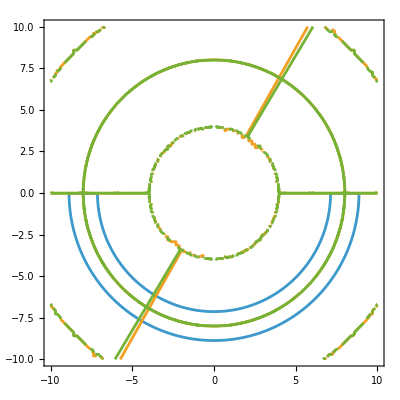

{x→-4.41475,y→-7.64657,vely→0.866025}

```mathematica
ClearAll[radius,sigma,DeflectorPushout,DeflectorSigmaFactor,u,k0];
radius=4;
sigma=4;
DeflectorPushout=1;
DeflectorSigmaFactor=1;

u=1/2;
k0=9/10;

ClearAll[funcs];
funcs={
vely+k0 f[radius+DeflectorPushout sigma-Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] f[-radius-DeflectorPushout sigma+Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] Sign[y]==0,
-1/(√(x^2+y^2))k0 vely ((-1+u^2) x+u vely y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0,
-1/(√(x^2+y^2))k0 vely (u vely x+(-1+vely^2) y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0
};

ClearAll[f];
f[x_,y0_,x0_,dx_]=polyTrans[x,y0,x0,dx];

ClearAll[funcsPlot];
funcsPlot=FullSimplify[funcs//.vely->86/100];

ContourPlot[
funcsPlot,
{x,-10,10},
{y,-10,10},
Exclusions->None,
PlotPoints->100
]

FindRoot[
funcs,
{x,-5},
{y,-8},
{vely,8/10}
]

ClearAll[funcsPlot];
ClearAll[f];
ClearAll[funcs];
ClearAll[rule];
ClearAll[radius,sigma,DeflectorPushout,DeflectorSigmaFactor,u,k0];
```

```mathematica
ClearAll[radius,sigma,DeflectorPushout,DeflectorSigmaFactor,u,k0];
radius=4;
sigma=4;
DeflectorPushout=1;
DeflectorSigmaFactor=19/10;

u=1/2;
k0=9/10;

ClearAll[funcs];
funcs={
vely+k0 f[radius+DeflectorPushout sigma-Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] f[-radius-DeflectorPushout sigma+Sqrt[x^2+y^2],1,0,DeflectorSigmaFactor sigma] Sign[y]==0,
-1/(√(x^2+y^2))k0 vely ((-1+u^2) x+u vely y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0,
-1/(√(x^2+y^2))k0 vely (u vely x+(-1+vely^2) y) Sign[y] (f[-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma]-f[radius+DeflectorPushout sigma-√(x^2+y^2),1,0,DeflectorSigmaFactor sigma] Derivative[1,0,0,0][f][-radius-DeflectorPushout sigma+√(x^2+y^2),1,0,DeflectorSigmaFactor sigma])==0
};

ClearAll[f];
f[x_,y0_,x0_,dx_]=polyTrans[x,y0,x0,dx];

ClearAll[funcsPlot];
funcsPlot=FullSimplify[funcs//.vely->86/100];

ClearAll[plotData];

Do[
plotData=ContourPlot[
Evaluate[funcsPlot[[i]]],
{x,-20,20},
{y,-20,20},
Exclusions->None,
PlotPoints->500
];
Export["../fixed_point_1/fixed_point_"<>ToString[i]<>".txt",plotData[[1,1,1]],"Table"]
,
{i,1,3}
];

ClearAll[plotData];
ClearAll[funcsPlot];
ClearAll[f];
ClearAll[funcs];
ClearAll[rule];
ClearAll[radius,sigma,DeflectorPushout,DeflectorSigmaFactor,u,k0];
```